1

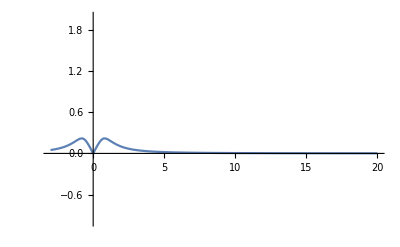

0

```mathematica
(*
Assuming our data is standardized with x values in [-1,1], reasonable length scales l should always be much smaller than 20,
in which case
Exp[-1/l^2]BesselI[0,1/l^2]
and
Exp[-1/l^2]BesselI[1,1/l^2]
are very well behaved and bounded by [0,1]
*)
(* Bessel 0 *)
Plot[Exp[-1/l^2]BesselI[0,1/l^2],{l,-3,20},PlotRange->{-1,2}]
Limit[Exp[-1/l^2]BesselI[0,1/l^2],l->∞]
(* Bessel 1 *)
Plot[Exp[-1/l^2]BesselI[1,1/l^2],{l,-3,20},PlotRange->{-1,2}]
Limit[Exp[-1/l^2]BesselI[1,1/l^2],l->∞]
```

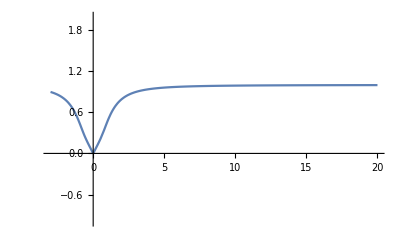

1

-Graphics-

0

```mathematica
0
```

1

-Graphics-

```mathematica
(*
the kernel is given by the following. Note that the Exp[1/l^2] terms blow up as l->0 (since 1/l^2 gets very large)
*)

kernelFn=(Exp[Cos[(2π dists)/p]/l^2]-BesselI[0,1/l^2])/(Exp[1/l^2]-BesselI[0,1/l^2])
```

(ⅇ^(Cos[(2 dists π)/p]/l^2)-BesselI[0,1/l^2])/(ⅇ^(1/l^2)-BesselI[0,1/l^2])

```mathematica
Manipulate[{Plot3D[kernelFn/.{dists->x,l->len,p->y},{x,0,2},{len,.01,3},PerformanceGoal->"Quality",MaxRecursion->3],
Plot3D[Exp[(-2 Sin[(2π dists)/p]^2)/l^2]/.{dists->x,l->len,p->y},{x,0,2},{len,.01,3},PerformanceGoal->"Quality",MaxRecursion->3]
},{y,0.001,3}]
```

```mathematica
(*
but this can be simplified using the more numerically stable formula above;
let 
expBess0 = Exp[-1/l^2]BesselI[0,1/l^2]
and
expBess1 = Exp[-1/l^2]BesselI[1,1/l^2]
*) 

rules = {
BesselI[0,1/l^2]->  ⅇ^(1/l^2)expBess0,
BesselI[1,1/l^2]-> ⅇ^(1/l^2) expBess1
};
kernelFnStable = kernelFn/.rules//FullSimplify
```

(-ⅇ^(-(2 Sin[(dists π)/p]^2)/l^2)+expBess0)/(-1+expBess0)

```mathematica
(-ⅇ^(-(2 Sin[(dists π)/p]^2)/l^2)+expBess0)/(-1+expBess0)==(-ⅇ^(-2(Sin[(dists π)/p]/l)^2)+expBess0)/(-1+expBess0)
```

True

```mathematica
(*
note that Sin[(dists π)/p]^2/l^2 is always positive, so -(2 Sin[(dists π)/p]^2)/l^2 is always negative, and thus 
0 < Exp[-(2 Sin[(dists π)/p]^2)/l^2] < 1.;

Though expBess0->1 as l->∞,for reasonable values of l (less than 5 or 10) we should hopefully not get too close to division by zero


Focusing on the derivative of the kernel WRT l, since that has been the problem. Lets simplify Cos[(2π dists)/p]->c, since this is held fixed when differntiating wrt l
*)

kernelFn2 = kernelFn/.{Cos[(2 π dists)/p]->c}
```

(ⅇ^(c/l^2)-BesselI[0,1/l^2])/(ⅇ^(1/l^2)-BesselI[0,1/l^2])

```mathematica
(ⅇ^(c/l^2)-BesselI[0,1/l^2])/(ⅇ^(1/l^2)-BesselI[0,1/l^2])
```

```mathematica
(*
then take the derivatives. As above, we can replace the bessel functions with Exp*Bessel

Treat the numerator and denominator separately, and 
*)
num = (Numerator[D[kernelFn2,l]//Simplify]/.rules)//FullSimplify

denom = (Denominator[D[kernelFn2,l]//Simplify]/.rules)//FullSimplify
```

2 ⅇ^(1/l^2) (ⅇ^(c/l^2) (1+c (-1+expBess0)-expBess1)+ⅇ^(1/l^2) (-expBess0+expBess1))

ⅇ^(2/l^2) (-1+expBess0)^2 l^3

```mathematica
(*
do a little bit of manual simplification that mathematics doesn't want to do
*)Reduce[(num/denom)==(2  (ⅇ^((c-1)/l^2) (1+c (-1+expBess0)-expBess1)+ (-expBess0+expBess1)))/((-1+expBess0)^2 l^3)]
```

True

```mathematica
(*
and a little bit more automatic simplification...
*)

dKdl3=(2  (ⅇ^((c-1)/l^2) (1+c (-1+expBess0)-expBess1)+ (-expBess0+expBess1)))/((-1+expBess0)^2 l^3)//FullSimplify
```

(2 (-expBess0+ⅇ^((-1+c)/l^2) (1+c (-1+expBess0)-expBess1)+expBess1))/((-1+expBess0)^2 l^3)

```mathematica
(*
Now note that since
-1 ≤ c = Cos[(2π dists)/p] ≤ 1;
then -2 ≤ c-1 ≤ 0, so;
(-1+c)/l^2 ≤0 for all l,
and therefore;
0 < Exp[(-1+c)/l^2] ≤ 1, so nothing here should blows up...


Finally, note that we need
2 Sin[(dists π)/p]^2
for the numerically stable kernel def above.

But Cos[2x] == 1-2 Sin[x]^2, so 
1-Cos[(2π dists)/p]==Sin[(dists π)/p]^2

so we can replace the computation of Cos and reuse the Sin

*)
```

```mathematica
cosRule = {c->1-2 Sin[(dists π)/p]^2}
Reduce[Cos[2(dists π)/p]==c/.cosRule,Reals]//Simplify

dKdl4 = dKdl3 /. cosRule
```

{c→1-2 Sin[(dists π)/p]^2}

True

1/((-1+expBess0)^2 l^3)2 (-expBess0+expBess1+ⅇ^(-(2 Sin[(dists π)/p]^2)/l^2) (1-expBess1+(-1+expBess0) (1-2 Sin[(dists π)/p]^2)))

```mathematica
(*
should also redo the period gradient to avoid Exp[1/l^2]
*)
```

```mathematica
dKdp =(D[kernelFn,p]/.rules)//FullSimplify
```

-(2 dists ⅇ^(-(2 Sin[(dists π)/p]^2)/l^2) π Sin[(2 dists π)/p])/((-1+expBess0) l^2 p^2)

```mathematica
(*
the final formulae
*)

kernelFnStable

dKdl4

dKdp
```

```mathematica
kernelFnStable/.{Sin[(dists π)/p]^2->S}

dKdl4/.{Sin[(dists π)/p]^2->S}

dKdp/.{ Sin[(dists π)/p]^2->S}
```

(-ⅇ^(-(2 S)/l^2)+expBess0)/(-1+expBess0)

(2 (-expBess0+expBess1+ⅇ^(-(2 S)/l^2) (1-expBess1+(-1+expBess0) (1-2 S))))/((-1+expBess0)^2 l^3)

```mathematica
-(2 dists ⅇ^(-(2 S)/l^2) π Sin[(2 dists π)/p])/((-1+expBess0) l^2 p^2)
```

```mathematica
kernelAndGrads=Function[({kernelFnStable,dKdl4,dKdp}/.{expBess0 -> Exp[-1/l^2]BesselI[0,1/l^2],
expBess1 -> Exp[-1/l^2]BesselI[1,1/l^2]})/.{dists->#1,l->#2,p->#3}];

kernelAndGrads[.1,.1,.1]
```

{kernelFnStable,dKdl4,dKdp}/.{expBess0→Exp[-1/l^2] BesselI[0,1/l^2],expBess1→Exp[-1/l^2] BesselI[1,1/l^2]}/.{dists→#1,l→#2,p→#3}&

{1.,-1.50566×10^-14,-1.60297×10^-12}

```mathematica
perms = Flatten[
Outer[List,
Range[-1,1,.1](*dists*),
{0.001,0.01,0.1,.5,1,2,4,8}(*l*),
{0.001,0.01,0.1,.5,1,2,4}](*p*),
2];

Length[perms]

testVals = Map[({kernelFn/.{dists->#1,l->#2,p->#3},#1,#2,#3})& @@ #&,perms];
Length[testVals]
testVals
```

1176

1176

{{1.,-1.,0.001,0.001},1174,{-0.00389095,1.,8,4}}
 |  |  |  |

```mathematica
testValsWithGrads = Map[({kernelAndGrads[#1,#2,#3],#1,#2,#3})& @@ #&,perms];
(*Map[kernelAndGrads@@#&,perms];*)
Length[testValsWithGrads]
testValsWithGrads
```

1176

{{{1.,4.57269×10^-9,-4.04065},-1.,0.001,0.001},1174,{{-0.00389095,0.000968904,0.391155},1.,8,4}}
 |  |  |  |

```mathematica
Export["testValsWithGrads.json",testValsWithGrads]
```

testValsWithGrads.json

```mathematica
N[Exp[-1/l^2]BesselI[0,1/l^2]/.l-> 3]
```

0.897603

```mathematica
NumberForm[0.06932006015460074,16]
```

0.06932006015460074